```mathematica
DSolve[{-(1/2)*y''[x] - a*y[x]== 0},y[x],x]




DSolve[{-y''[x] - a*y[x]== 0,y'[0]==0, y'[Sqrt[2]]==(Sqrt[2]-1/Sqrt[2])/2},y[x],x]
```

{{y[x]→C[1] Cos[√2 √a x]+C[2] Sin[√2 √a x]}}

{{y[x]→-(Cos[√a x] Csc[√2 √a])/(2 √2 √a)}}

```mathematica
gh[0,-0.39]
```

gh[0,-0.39]

```mathematica
{1.9641855032959683,7.071067811865484,-1.4142135623730965}
```

{1.96419,7.07107,-1.41421}

ParametricFunction[<>]

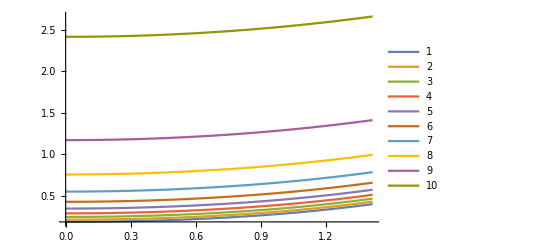

```mathematica
pfunfin=ParametricNDSolveValue[{ -y''[x]==Ei*y[x],y'[0]==0,y'[Sqrt[2]]==(Sqrt[2]-1/Sqrt[2])/2},y,{x,0,Sqrt[2]},{Ei}]
Show[Plot[Evaluate@Table[Re[pfunfin[Ei][x]],{Ei,-1,-0.1,0.1}],{x,0,Sqrt[2]},PlotLegends->Automatic],PlotRange->All]
```

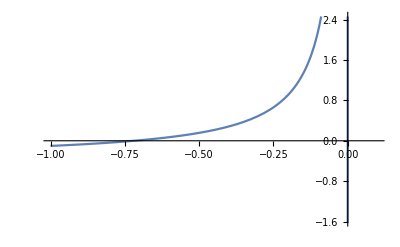

```mathematica
Plot[pfunfin[Ei][Sqrt[2]]-0.5,{Ei,-1,0.1}]
```

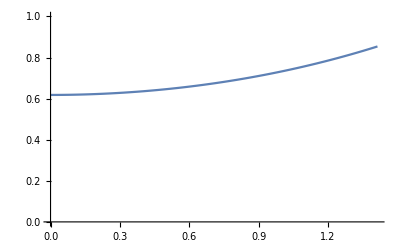

```mathematica
Plot[pfunfin[-0.359807336][x],{x,0, Sqrt[2]}, PlotRange->{{0, Sqrt[2]},{0, 1}}]
```

```mathematica
res1=FindRoot[pfunfin[Ei][Sqrt[2]]-1/2,{Ei,-0.4}, AccuracyGoal->100, WorkingPrecision->100]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 100. digits of working precision to meet these tolerances.

{Ei→-0.7196144405439598437630947298474546767136894639307686018182808990592700403575208595626554096360208898}

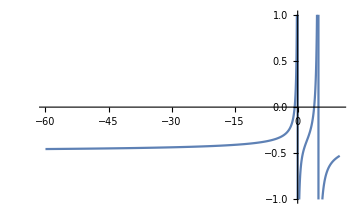

```mathematica
Plot[pfunfin[Ei][Sqrt[2]]-0.5,{Ei,-60,10},ImageSize->Medium, PlotRange->{{-60,10},{-1,1}}]
```

```mathematica
val1=Map[FindRoot[pfunfin[Ei][0]-1,{Ei,-0.4}, AccuracyGoal->100, WorkingPrecision->100]&,{1,2,3}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 100. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{Ei→-0.2316877630677504564941833503208436618616300990009459863115676794451280949710673875563169050812631452},{Ei→-0.2316877630677504564941833503208436618616300990009459863115676794451280949710673875563169050812631452},{Ei→-0.2316877630677504564941833503208436618616300990009459863115676794451280949710673875563169050812631452}}

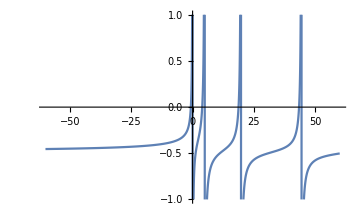

```mathematica
Plot[pfunfin[Ei][Sqrt[2]]-0.5,{Ei,-60,60},ImageSize->Medium, PlotRange->{{-60,60},{-1,1}}, Exclusions->1/D[pfunfin[Ei][Sqrt[2]],Ei]==0,Exclusions->{1/pfunfin[Ei][Sqrt[2]]==0}]
```

```mathematica
(*Function Definition*)pl[f_,lims_]:=Plot[f[u],{u,lims[[1]],lims[[2]]},Exclusions->{(f[u]-f[u+0.1])/.1==10,(f[u]-f[u+0.1])/.1==-10}];
pl1[f_,lims_]:=Plot[f[u],{u,lims[[1]],lims[[2]]}];
```

```mathematica
pfutest[x_]:=pfunfin[x][Sqrt[2]]-0.5
```

ParametricNDSolveValue::prange: Invalid non-numeric value 0.1+u for parameter Ei.

General::stop: Further output of ParametricNDSolveValue::prange will be suppressed during this calculation.

Hold::prange: -- Message text not found -- (Ei) (0.1+Charting`Private`pvar$1717052)

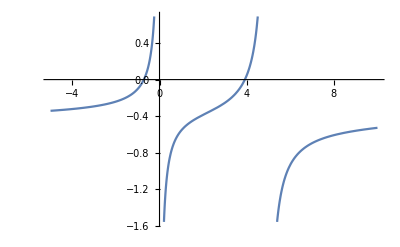

```mathematica
pl[pfutest, {-5,10}]
```

ParametricNDSolveValue::prange: Invalid non-numeric value 0.1+u for parameter Ei.

General::stop: Further output of ParametricNDSolveValue::prange will be suppressed during this calculation.

Hold::prange: -- Message text not found -- (Ei) (0.1+Charting`Private`pvar$1889310)

ParametricNDSolveValue::berr: The scaled boundary value residual error of 4.11633 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

ParametricNDSolveValue::berr: The scaled boundary value residual error of 3.69438 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

ParametricNDSolveValue::berr: The scaled boundary value residual error of 1.40496 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

General::stop: Further output of ParametricNDSolveValue::berr will be suppressed during this calculation.

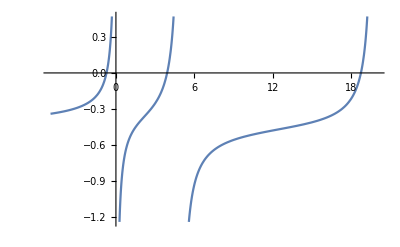

```mathematica
pl[pfutest, {-5,20}]
```

```mathematica
Plot[f[u],{u,lims[[1]],lims[[2]]},Exclusions->{(f[u]-f[u+0.1])/.1==10,(f[u]-f[u+0.1])/.1==-10}]
```

Part::partd: Part specification lims⟦1⟧ is longer than depth of object.

Part::partd: Part specification lims⟦2⟧ is longer than depth of object.

Plot::plln: Limiting value lims⟦1⟧ in {u,lims⟦1⟧,lims⟦2⟧} is not a machine-sized real number.

Plot[f[u],{u,lims⟦1⟧,lims⟦2⟧},Exclusions→{(f[u]-f[u+0.1])/0.1==10,(f[u]-f[u+0.1])/0.1==-10}]